```mathematica
ClearAll["Global`*"]
```

```mathematica
f[x_,y_]:=Sin[2Pi x] Sin[2Pi y]
```

```mathematica
Plot3D[f[x,y],{x,0,1},{y,0,1}]
```

-Graphics3D-

```mathematica
dfdx = D[f[x,y],x]
```

2 π Cos[2 π x] Sin[2 π y]

```mathematica
dfdy = D[f[x,y],y]
```

2 π Cos[2 π y] Sin[2 π x]

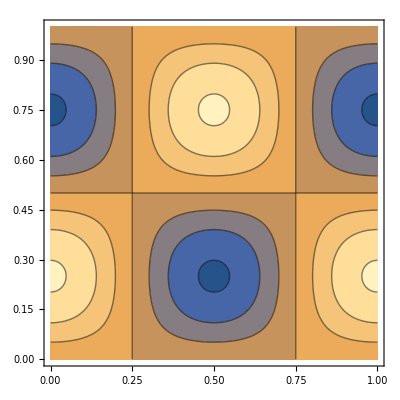

-Graphics3D-

```mathematica
ContourPlot[dfdx,{x,0,1},{y,0,1}]
Plot3D[dfdx,{x,0,1},{y,0,1}]
```

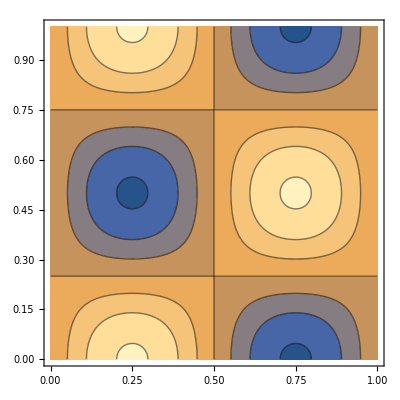

```mathematica
ContourPlot[dfdy,{x,0,1},{y,0,1}]
```